```mathematica
(*1. Ellenőrizzük a (2)-(5) egyenleteket. *)

(* 2 *)Simplify[Integrate[Sin[n*Pi*x/a]*Sin[m*Pi*x/a],{x,-a,a}],Element[{m,n},Integers]]
(* 2 *)Simplify[Integrate[Sin[n*Pi*x/a]*Sin[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]

(* 3 *)Simplify[Integrate[Sin[n*Pi*x/a]*Cos[m*Pi*x/a],{x,-a,a}],Element[{m,n},Integers]]
(* 3 *)(*Simplify[Integrate[Sin[n*Pi*x/a]*Cos[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]*)

(* 4 *)Simplify[Integrate[Sin[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]
(* 5 *)Simplify[Integrate[Cos[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]
```

0

a

0

0

0

«1 more identical outputs»

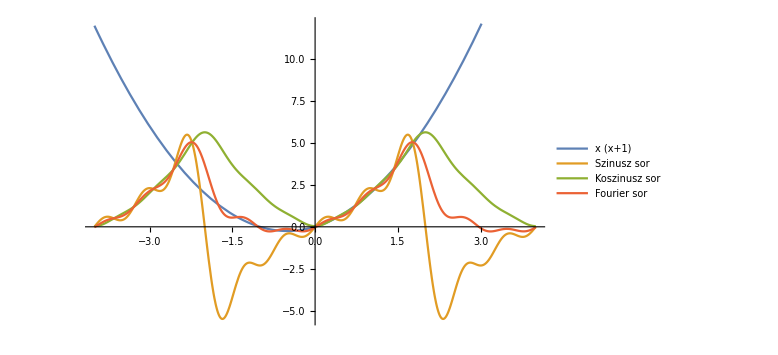

```mathematica
(*2.a. Írjuk meg a fourierSinCoefficient[f,x,m,a] függvényt,ami megadja azf(x)kifejezés(0,a)intervallumon vett szinusz soránakm-edik együtthatóját*)
fourierSinCoefficient[f_,x_,m_,a_] := 2/a* Integrate[f[x]*Sin[m*Pi*x/a], {x, 0, a}]
(* ..../; m == 0*)

(*2.a. Írjuk meg a fourierSinCoefficient[f,x,m,a] függvényt,ami megadja azf(x)kifejezés(0,a)intervallumon vett koszinusz soránakm-edik együtthatóját*)
(*fourierCosCoefficient[f_,x_,m_,a_] := 1/a*Integrate[f[x],{x, 0, a}]/;m==0
fourierCosCoefficient[f_,x_,m_,a_] := 2/a* Integrate[f[x]*Cos[m*Pi*x/a], {x, 0, a}]/;m≠0
*)
fourierCosCoefficient[f_,x_,m_,a_] :=If[m==0,1/a*Integrate[f[x],{x, 0, a}],2/a* Integrate[f[x]*Cos[m*Pi*x/a], {x, 0, a}]]



fourierTrigCoefficient[f_,x_,m_,a_,sc_]:=
If[sc==0,
If[m==0, 1/2/a*Integrate[f[x],{x,-a,a}],
1/a*Integrate[f[x]*Cos[m*Pi*x/a],{x,-a,a}]
],
1/a*Integrate[f[x]*Sin[m*Pi*x/a],{x,-a,a}]
];

(*2.c. *)
f[x_] = x(x+1);

fsin[f_,x_]=Sum[fourierSinCoefficient[f, x, n, 2]*Sin[n*Pi*x/2], {n, 0, 5}];
fcos[f_,x_]=Sum[fourierCosCoefficient[f, x, n, 2]*Cos[n*Pi*x/2], {n, 0, 5}];
ffourier[f_,x_]=Sum[fourierTrigCoefficient[f, x, n, 2, 0]*Cos[n*Pi*x/2]+fourierTrigCoefficient[f, x, n, 2, 1]*Sin[n*Pi*x/2], {n,0,5}];

Plot[{
f[x],
fsin[f,x],
fcos[f,x],
ffourier[f,x]
}, {x, -4, 4},
PlotLegends->{f[x],"Szinusz sor", "Koszinusz sor","Fourier sor" },
ImageSize->Large
]
```

```mathematica
(*3. feladat *)
sol3=DSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}],
u[0,x]==x*(1-x),
u[t,0]==0,
u[t,1]==0},u,{t,x}]/.{Infinity->10}//Activate;
plotSol3=Plot3D[sol3[t,x],{t,0,0.5},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];
```

```mathematica
g[x_]=x(1-x);
u10=Sum[fourierSinCoefficient[g,x,n,1]  * Sin[n*Pi*x]*Exp[-(n*Pi)^2*t],{n,1,10}];
plotU10=Plot3D[u10,{t,0,0.5},{x,0,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];
Show[plotSol3, plotU10]
```

-Graphics3D-

```mathematica
(*4. Feladat *)
g4[x_]=x(1-x);
f4[t_,x_]=t^2*x*(1-x);
a=1;
fn4[t_,n_]=2/a*Integrate[f4[t,x]*Sin[n*Pi*x],{x,0,1}];
(*fn4[t,n]*)

un4=DSolveValue[
{D[un4[t,n],t]+Pi^2*n^2*un4[t,n]==fn4[t,n],
un4[0,n]==fourierSinCoefficient[g4,x,n,1]}
,un4,{t}]

(*un4[t_,n_]=DSolveValue[
{un4'[t]+Pi^2*n^2*un4[t]==fn4[t,n],
un4[0]==2/a*Integrate[g4[x]*Sin[n*Pi*x],{x,0,1}]},
un4[t],t];*)
(*un4[t,n]*)

(*u4[t_,x_]=Sum[un4[t,n]*Sin[n*Pi*x],{n,1,10}];
Plot3D[u4[t,x],{t,0,5},{x,0,1}]*)
```

```mathematica
(*5. Feladat *)
g5[x_]=x(1-x);
f5[t_,x_]=t*x;
h1[t_]=t;
h2[t_]=2t;
v[t_,x_]=(h2[t]-h1[t])*x+h1[t];
```

```mathematica
(* OK *)
(* 6. Feladat *)
g6[x_]=x(1-x);
u6=Sum[fourierCosCoefficient[g6,x,n,1]  * Cos[n*Pi*x]*Exp[-(n*Pi)^2*t],{n,0,10}];
plotU6=Plot3D[u6,{t,0,0.2},{x,0,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];

sol6=DSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}],
u[0,x]==x*(1-x),
(D[u[t,x],x]/.{x->0})==0,
(D[u[t,x],x]/.{x->1})==0},u,{t,x}]/.{Infinity->10}//Activate;
plotSol6=Plot3D[sol6[t,x],{t,0,0.2},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];

Show[plotU6, plotSol6]
```

DSolve::ivar: Cos is not a valid variable.

-Graphics3D-

```mathematica
(* 7. Feladat *)
g7[x_]=(1+x)*(1-x);
u7=Sum[(fourierTrigCoefficient[g7,x,n,1,0]  * Cos[n*Pi*x]
+fourierTrigCoefficient[g7,x,n,1,1]  * Sin[n*Pi*x])
*Exp[-(n*Pi)^2*t],{n,0,10}
];
plotU7=Plot3D[u7,{t,0,0.2},{x,-1,1}
,PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Magenta,Opacity[0.8]}];

sol7=NDSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}],
u[0,x]==(1-x)(1+x),
PeriodicBoundaryCondition[u[t,x],x==-1,Function[z,z+2]]
},u,{t,0,1},{x,-1,1}];
plotSol7=Plot3D[sol7[t,x],{t,0,0.2},{x,-1,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];

Show[plotU7, plotSol7]
```

NDSolveValue::dsfun: 1/6-(ⅇ^(-4 π^2 t) Cos[2 π x])/π^2-(ⅇ^(-16 π^2 t) Cos[4 π x])/(4 π^2)-(ⅇ^(-36 π^2 t) Cos[6 π x])/(9 π^2)-(ⅇ^(-64 π^2 t) Cos[8 π x])/(16 π^2)-(ⅇ^(-100 π^2 t) Cos[10 π x])/(25 π^2) cannot be used as a function.

NDSolveValue::dsvar: 0.0000143 cannot be used as a variable.

NDSolveValue::dsvar: 0.0143 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics3D-